```mathematica
f[x_,y_]= Exp[x+y]
```

ⅇ^(x+y)

```mathematica
phiTri[a_,b_,c_,{x_,y_}]:=Module[{p,α,β},
{α,β}=LinearSolve[{{Norm[b-a]^2,(b-a).(c-a)},{(b-a).(c-a),Norm[c-a]^2}},{-1,-1}];
p = α (b-a) + β (c-a);
Return[1 + p.({x,y}-a)]
]
```

```mathematica
phiRef[x_,y_]={1-x-y,x,y}
```

{-x-y+1,x,y}

```mathematica
gradPhiRef[x_,y_]={D[phiRef[x,y],x],D[phiRef[x,y],y]}
```

(-1 | 1 | 0
-1 | 0 | 1)

```mathematica
phiProdRef[x_,y_]=KroneckerProduct[phiRef[x,y],phiRef[x,y]]
```

((-x-y+1)^2 | x (-x-y+1) | y (-x-y+1)
x (-x-y+1) | x^2 | x y
y (-x-y+1) | x y | y^2)

```mathematica
{aa, bb, cc}={{-1/4,1/8},{5/4,0},{1,4/3}}
```

(-1/4 | 1/8
5/4 | 0
1 | 4/3)

```mathematica
J =Transpose[ {bb-aa,cc-aa}]
```

(3/2 | 5/4
-1/8 | 29/24)

```mathematica
gradPhiPhys[x_,y_]=Inverse[Transpose[J]].gradPhiRef[x,y]
```

(-128/189 | 116/189 | 4/63
-8/63 | -40/63 | 16/21)

```mathematica
laplPhys[x_,y_]=Transpose[gradPhiPhys[x_,y_]].gradPhiPhys[x,y]
```

(16960/35721 | -11968/35721 | -1664/11907
-11968/35721 | 27856/35721 | -5296/11907
-1664/11907 | -5296/11907 | 2320/3969)

```mathematica
Total[laplPhys[x,y]]
```

{0,0,0}

```mathematica
phiPhys[x_,y_]={phiTri[aa,bb,cc,{x,y}],phiTri[bb,cc,aa,{x,y}],phiTri[cc,aa,bb,{x,y}]}
```

{-128/189 (x+1/4)-8/63 (y-1/8)+1,116/189 (x-5/4)-(40 y)/63+1,(4 (x-1))/63+16/21 (y-4/3)+1}

```mathematica
R = Triangle[{{0,0},{1,0},{0,1}}]
```

Triangle[(0 | 0
1 | 0
0 | 1)]

```mathematica
T = Triangle[{aa,bb,cc}]
```

Triangle[(-1/4 | 1/8
5/4 | 0
1 | 4/3)]

```mathematica
fileNum = "9"
```

9

```mathematica
refQP = Import["/Users/katharine/Projects/PyPDE/Agnes/Quadrature/strang"<>fileNum <> "_x.txt", "Table"]
```

(0.873822 | 0.063089
0.063089 | 0.873822
0.063089 | 0.063089
0.501427 | 0.249287
0.249287 | 0.501427
0.249287 | 0.249287
0.636502 | 0.310352
0.636502 | 0.053145
0.310352 | 0.636502
0.310352 | 0.053145
0.053145 | 0.636502
0.053145 | 0.310352)

```mathematica
physQP = Table[aa + (bb -aa)p[[1]] + (cc-aa)p[[2]],{p,refQP}]
```

(1.13959 | 0.0920048
0.936911 | 1.17298
-0.0765052 | 0.193346
0.813748 | 0.363543
0.750713 | 0.69973
0.435539 | 0.395061
1.09269 | 0.420446
0.771185 | 0.109654
1.01116 | 0.855313
0.28196 | 0.150423
0.625346 | 0.887464
0.217658 | 0.493366)

```mathematica
w = Flatten[Import["/Users/katharine/Projects/PyPDE/Agnes/Quadrature/strang"<> fileNum <>"_w.txt", "Table"]]
```

{0.0508449,0.0508449,0.0508449,0.116786,0.116786,0.116786,0.0828511,0.0828511,0.0828511,0.0828511,0.0828511,0.0828511}

```mathematica
Qex=Integrate[f[x,y]laplPhys[x,y], {x, y}∈ T]//N
```

(1.67324 | -1.18074 | -0.4925
-1.18074 | 2.74821 | -1.56748
-0.4925 | -1.56748 | 2.05998)

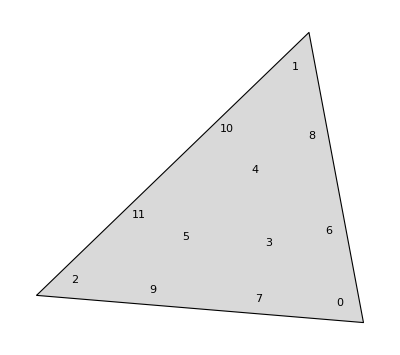

```mathematica
Graphics[{FaceForm[LightGray],EdgeForm[Black],T,Table[Text[i-1,physQP[[i]]],{i,1,Length[physQP]}]}]
```

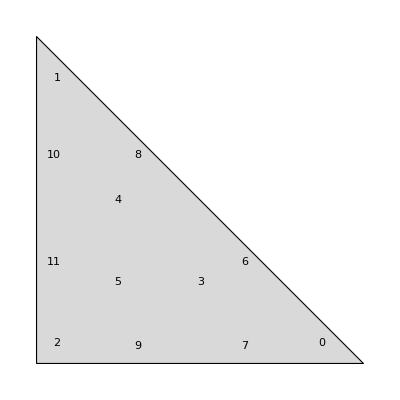

```mathematica
Graphics[{FaceForm[LightGray],EdgeForm[Black],R,Table[Text[i-1,refQP[[i]]],{i,1,Length[refQP]}]}]
```

```mathematica
fVals = f[physQP[[;;,1]],physQP[[;;,2]]]
```

{3.4267,8.24736,1.12394,3.24557,4.265,2.29469,4.54097,2.41292,6.46543,1.54092,4.53947,2.03608}

```mathematica
wf = w fVals
```

{0.17423,0.419336,0.0571467,0.379038,0.498094,0.267989,0.376224,0.199913,0.535668,0.127667,0.3761,0.168691}

```mathematica
Qphys= Total[wf]laplPhys[x,y] Area[T]
```

(1.67324 | -1.18074 | -0.4925
-1.18074 | 2.74821 | -1.56748
-0.4925 | -1.56748 | 2.05998)

```mathematica
Qex
```

(1.67324 | -1.18074 | -0.4925
-1.18074 | 2.74821 | -1.56748
-0.4925 | -1.56748 | 2.05998)

```mathematica
Qphys - Qex
```

(-2.55292×10^-7 | 1.8015×10^-7 | 7.51426×10^-8
1.8015×10^-7 | -4.19305×10^-7 | 2.39156×10^-7
7.51426×10^-8 | 2.39156×10^-7 | -3.14298×10^-7)